# Diplomado en programación MCTP

Luis Gerardo Ramirez Archundia

22/02/2023

Use RegularPolygon para dibujar un triángulo.

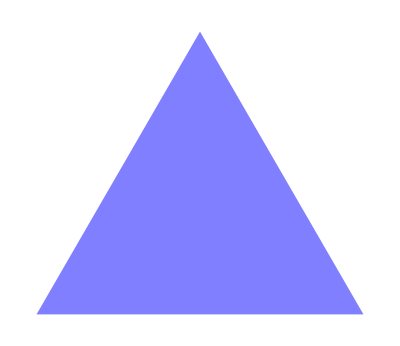

```mathematica
Graphics[Style[RegularPolygon[3], Blue, Opacity[0.5]]]
```

Dibuje el gráfico de un círculo rojo.



```mathematica
Graphics[Style[Disk[{0,0},1],Red]]
```

Muestre un octágono rojo

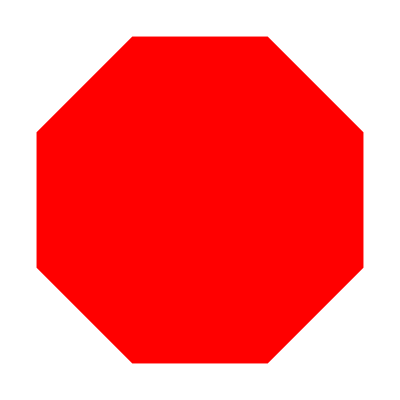

```mathematica
Graphics[Style[RegularPolygon[8],Red]]
```

Muestre una columna con un triángulo rojo y otro verde.

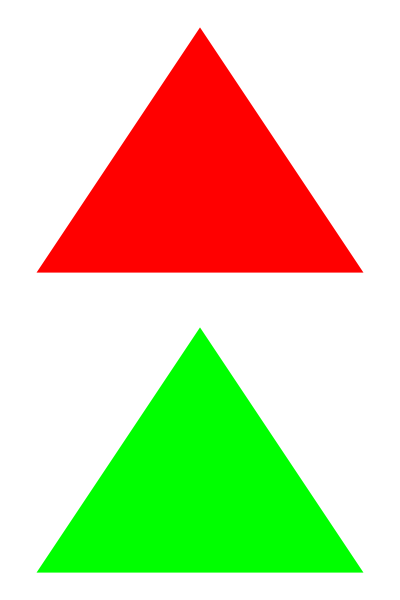

```mathematica
{Graphics[Style[RegularPolygon[3],Red]],Graphics[Style[RegularPolygon[3],Green]]}//Column
```

Forme una lista de 10 pentágonos rosas.

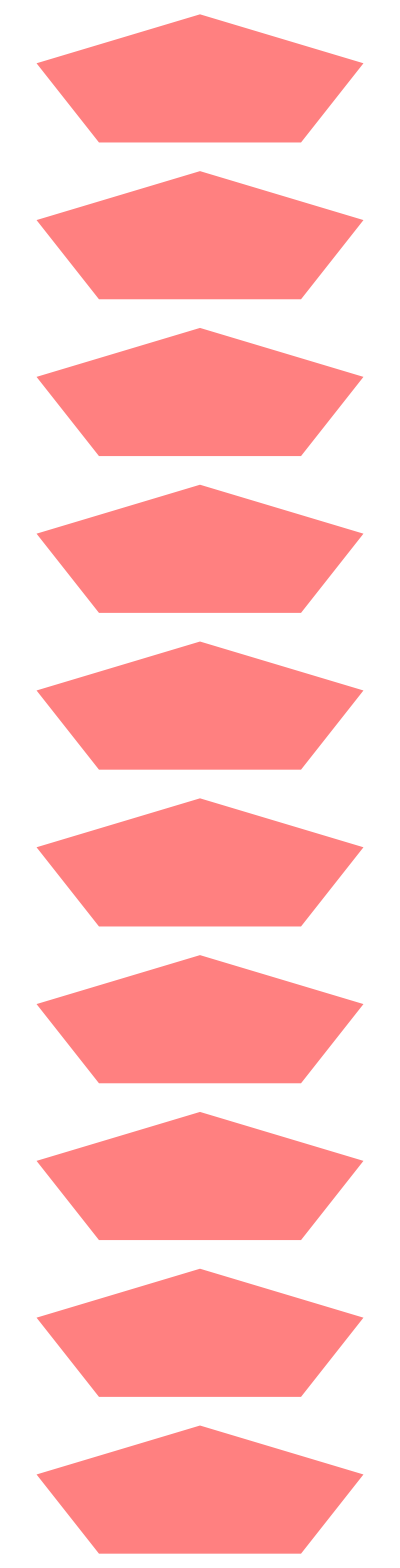

```mathematica
Table[Graphics[Style[RegularPolygon[5],Pink]],10]//Column
```

Cree una lista de polígonos con 10, 9, ... , 3 lados.



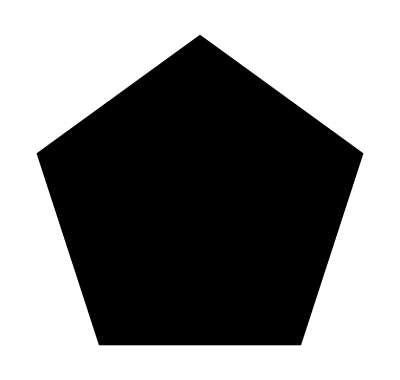
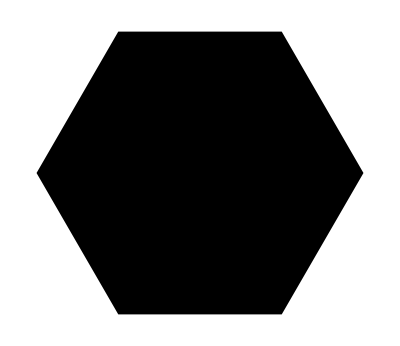
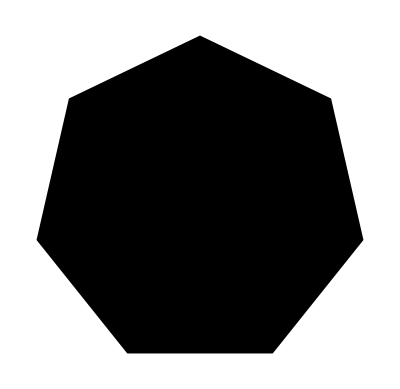
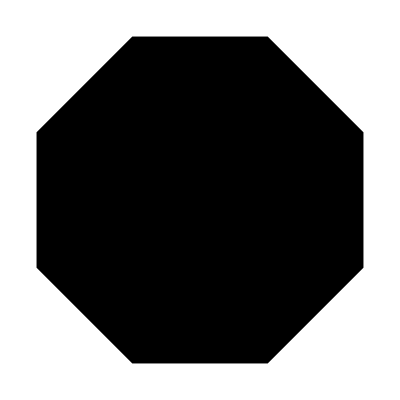
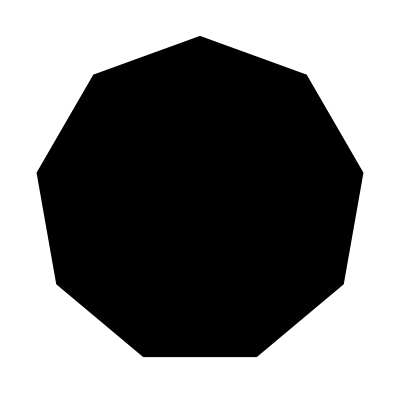
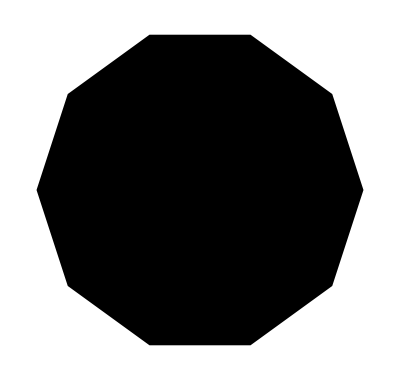

```mathematica
Table[Graphics[Style[RegularPolygon[n]]],{n,3,10}]
```

Muestre el gráfico de un cilindro morado.

```mathematica
Graphics3D[Style[Cylinder[], Purple]]
```

-Graphics3D-

Construya un Manipulate que muestre Range[n] para los valores de n entre 0 y 100.

```mathematica
Manipulate[Range[n],{n,0,100}]
```

Construya un Circulo que vaya creciendo con el radio de 1 a 100.

```mathematica
Manipulate[Graphics[Style[Circle[{0,0},r]],Axes->True],{r,1,100}]
```

Construir un gráfico de cos(x(1 + ax)) donde a varia de 0, 10 con Manipulate.

```mathematica
Manipulate[Plot[Cos[x(1+a*x)],{x,-Pi,Pi}],{a,1,10}]
```

Construir un esfera con 3 esferas dentro que vayan creciendo de radio (de 1 a 20). El circulo color azul
y las esferas, una verde,otra roja y la última amarilla.

```mathematica
quarks=Manipulate[Graphics3D[Style[{Sphere[{0,0,0},50],Red,Sphere[{-10,-15,15},r1],Blue,Sphere[{10,3,20},r2],Green,Sphere[{10,-10,-20},r3]}, Opacity[0.3]],
 Axes->True, AxesLabel->{x,y,z}],{r1,1,20,0.5},{r2,1,15,0.5},{r3,1,10,0.5}]
```

Hacer una tabla de nx y sin(nx) donde n varía de 0 a 100.

```mathematica
Table[{n*x,Sin[n x]},{n,0,100}]//TableForm
```

0 | 0
x | Sin[x]
2 x | Sin[2 x]
3 x | Sin[3 x]
4 x | Sin[4 x]
5 x | Sin[5 x]
6 x | Sin[6 x]
7 x | Sin[7 x]
8 x | Sin[8 x]
9 x | Sin[9 x]
10 x | Sin[10 x]
11 x | Sin[11 x]
12 x | Sin[12 x]
13 x | Sin[13 x]
14 x | Sin[14 x]
15 x | Sin[15 x]
16 x | Sin[16 x]
17 x | Sin[17 x]
18 x | Sin[18 x]
19 x | Sin[19 x]
20 x | Sin[20 x]
21 x | Sin[21 x]
22 x | Sin[22 x]
23 x | Sin[23 x]
24 x | Sin[24 x]
25 x | Sin[25 x]
26 x | Sin[26 x]
27 x | Sin[27 x]
28 x | Sin[28 x]
29 x | Sin[29 x]
30 x | Sin[30 x]
31 x | Sin[31 x]
32 x | Sin[32 x]
33 x | Sin[33 x]
34 x | Sin[34 x]
35 x | Sin[35 x]
36 x | Sin[36 x]
37 x | Sin[37 x]
38 x | Sin[38 x]
39 x | Sin[39 x]
40 x | Sin[40 x]
41 x | Sin[41 x]
42 x | Sin[42 x]
43 x | Sin[43 x]
44 x | Sin[44 x]
45 x | Sin[45 x]
46 x | Sin[46 x]
47 x | Sin[47 x]
48 x | Sin[48 x]
49 x | Sin[49 x]
50 x | Sin[50 x]
51 x | Sin[51 x]
52 x | Sin[52 x]
53 x | Sin[53 x]
54 x | Sin[54 x]
55 x | Sin[55 x]
56 x | Sin[56 x]
57 x | Sin[57 x]
58 x | Sin[58 x]
59 x | Sin[59 x]
60 x | Sin[60 x]
61 x | Sin[61 x]
62 x | Sin[62 x]
63 x | Sin[63 x]
64 x | Sin[64 x]
65 x | Sin[65 x]
66 x | Sin[66 x]
67 x | Sin[67 x]
68 x | Sin[68 x]
69 x | Sin[69 x]
70 x | Sin[70 x]
71 x | Sin[71 x]
72 x | Sin[72 x]
73 x | Sin[73 x]
74 x | Sin[74 x]
75 x | Sin[75 x]
76 x | Sin[76 x]
77 x | Sin[77 x]
78 x | Sin[78 x]
79 x | Sin[79 x]
80 x | Sin[80 x]
81 x | Sin[81 x]
82 x | Sin[82 x]
83 x | Sin[83 x]
84 x | Sin[84 x]
85 x | Sin[85 x]
86 x | Sin[86 x]
87 x | Sin[87 x]
88 x | Sin[88 x]
89 x | Sin[89 x]
90 x | Sin[90 x]
91 x | Sin[91 x]
92 x | Sin[92 x]
93 x | Sin[93 x]
94 x | Sin[94 x]
95 x | Sin[95 x]
96 x | Sin[96 x]
97 x | Sin[97 x]
98 x | Sin[98 x]
99 x | Sin[99 x]
100 x | Sin[100 x]

Hacer un gráfico de barras con la lista: a, a2, a3. . . a10, donde a va de 0 a 10. Usar Manipulate.

```mathematica
Manipulate[BarChart3D[Table[a^n,{n,0,10}]],{a,1,10,1}]
```